```mathematica
I1=1;
I3=2;
m=1;
g=9.8;
l=1;
L=(I1/2)*(θ'[t]^2+ϕ'[t]^2*Sin[θ[t]]^2)+(I3/2)*(ψ'[t]+ϕ'[t]*Cos[θ[t]])^2-m*g*l*Cos[θ[t]];eo={D[L,θ[t]]==D[D[L,θ'[t]],t],D[L,ϕ[t]]==D[D[L,ϕ'[t]],t],D[L,ψ[t]]-0.08==D[D[L,ψ'[t]],t]};
bu={θ[0]==0.5,θ'[0]==0,ϕ[0]==0,ϕ'[0]==0,ψ[0]==0,ψ'[0]==10};
so=NDSolve[{eo,bu},{θ,ϕ,ψ},{t,0,50}]
```

{{θ→InterpolatingFunction[…],ϕ→InterpolatingFunction[…],ψ→InterpolatingFunction[…]}}

```mathematica
theta[t_]=First[θ[t]/.so]
phi[t_]=First[ϕ[t]/.so]
psi[t_]=First[ψ[t]/.so]
x[t_]=l*Sin[theta[t]]*Cos[phi[t]]
y[t_]=l*Sin[theta[t]]*Sin[phi[t]]
z[t_]=l*Cos[theta[t]]
```

InterpolatingFunction[…][t]

InterpolatingFunction[…][t]

InterpolatingFunction[…][t]

Cos[InterpolatingFunction[…][t]] Sin[InterpolatingFunction[…][t]]

Sin[InterpolatingFunction[…][t]] Sin[InterpolatingFunction[…][t]]

Cos[InterpolatingFunction[…][t]]

```mathematica
ParametricPlot3D[{x[t],y[t],z[t]},{t,0,50},BoxRatios->Automatic]
```

-Graphics3D-

```mathematica
Animate[Graphics3D[{{Thickness[0.01],Blue,Line[{{0,0,0},{x[t],y[t],z[t]}}]},Ball[{x[t],y[t],z[t]},0.08]},PlotRange->{{-1.5,1.5},{-1.5,1.5},{-0.1,1.1}}],{t,0,50},AnimationRunning->False,AnimationRate->1]
```

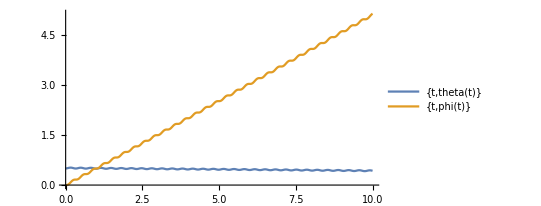

```mathematica
ParametricPlot[{{t,theta[t]},{t,phi[t]}},{t,0,10},PlotLegends->"Expressions"]
```

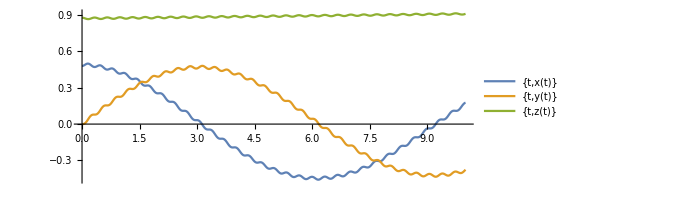

```mathematica
ParametricPlot[{{t,x[t]},{t,y[t]},{t,z[t]}},{t,0,10},PlotLegends->"Expressions"]
```

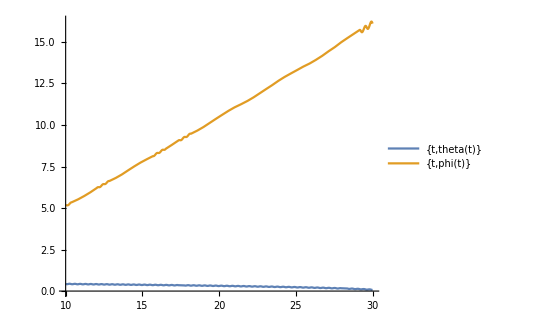

```mathematica
ParametricPlot[{{t,theta[t]},{t,phi[t]}},{t,10,30},PlotLegends->"Expressions"]
```

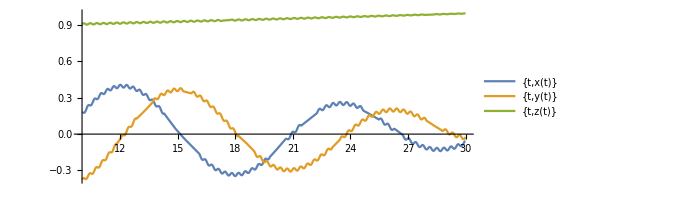

```mathematica
ParametricPlot[{{t,x[t]},{t,y[t]},{t,z[t]}},{t,10,30},PlotLegends->"Expressions"]
```

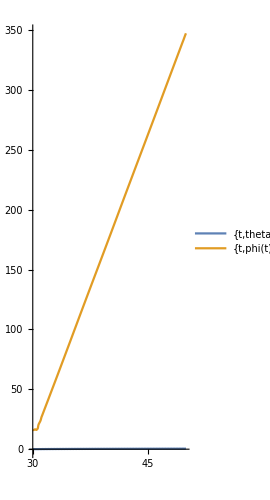

```mathematica
ParametricPlot[{{t,theta[t]},{t,phi[t]}},{t,30,50},PlotLegends->"Expressions"]
```

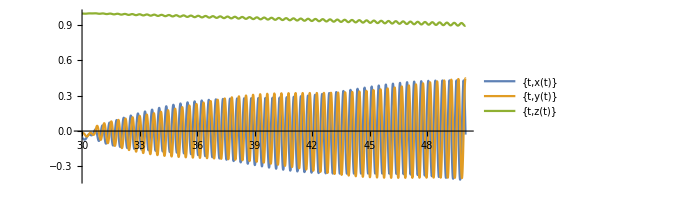

```mathematica
ParametricPlot[{{t,x[t]},{t,y[t]},{t,z[t]}},{t,30,50},PlotLegends->"Expressions"]
```

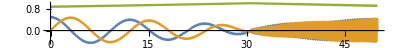

```mathematica
ParametricPlot[{{t,x[t]},{t,y[t]},{t,z[t]}},{t,0,50},PlotLegends->"Expressions",AspectRatio->0.1]
```